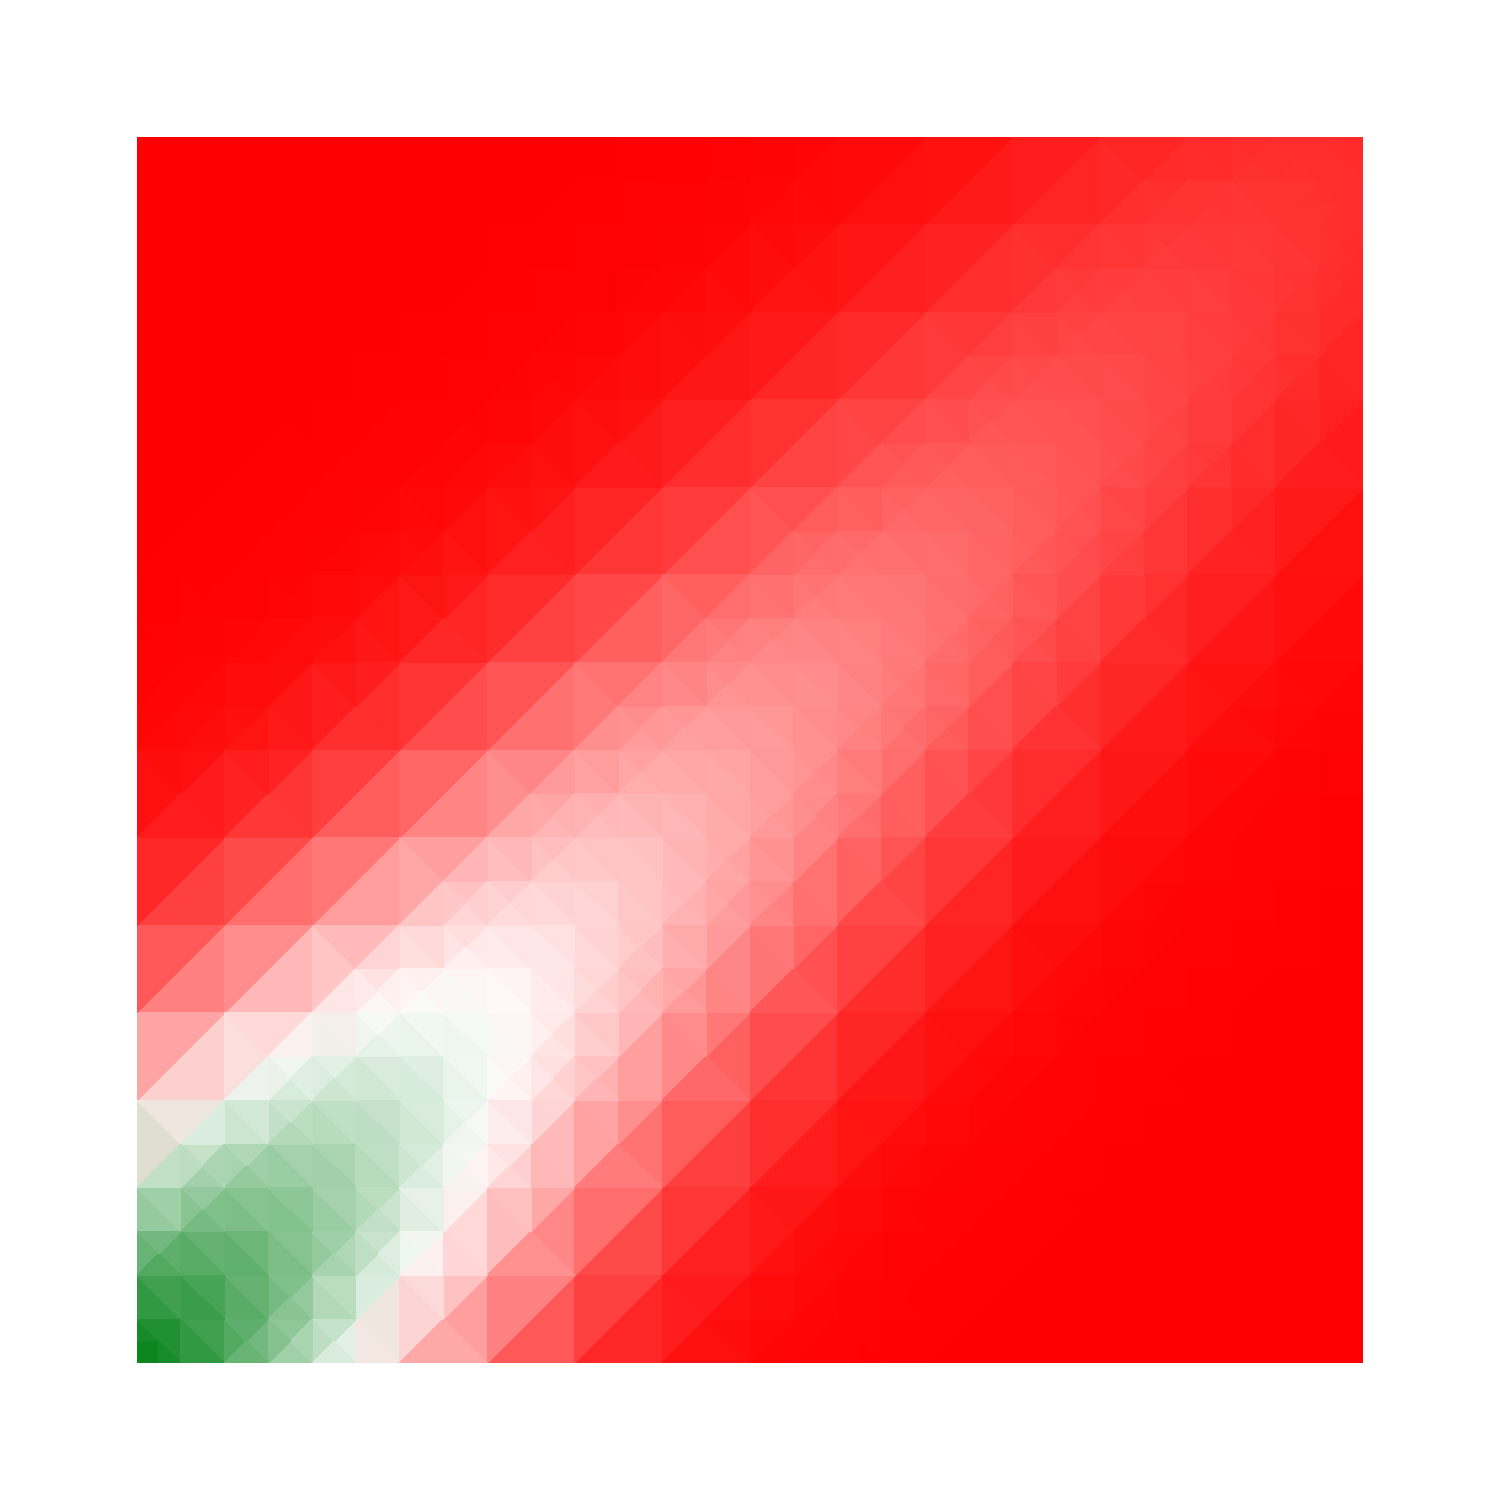

```mathematica
g[x_,y_]:=Exp[-15(x- y)^2]Sqrt[x+y+1] E^(x+y);
DensityPlot[g[1-x,1-y],{x,0,1},{y,0,1},PlotRange-> All,ImageSize-> {1500,1500},ColorFunction-> ColorData["Gradients"][[39]],Ticks-> None,Axes-> False,Frame-> False]
```